Exercises for Section 6 | Making Tables

Make a list in which the number 1000 is repeated 5 times. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

Make a table of the values of n^3 for n from 10 to 20. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

Make a number line plot of the first 20 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

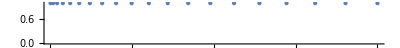

```mathematica
NumberLinePlot[Table[n^2,{n,1,20}]]
```

Make a list of the even numbers (2, 4, 6, ...) up to 20. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[n+2,{n,0,18,2}]
```

{2,4,6,8,10,12,14,16,18,20}

Use Table to get the same result as Range[10]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Range[10]
Table[n,{n,1,10,1}]
```

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

Make a bar chart of the first 10 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

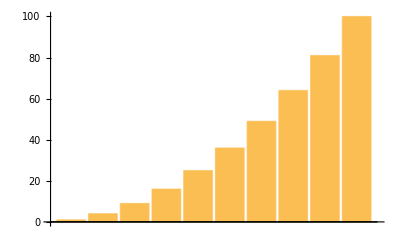

```mathematica
BarChart[Table[n^2,{n,1,10,1}]]
```

Make a table of lists of digits for the first 10 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[IntegerDigits[n^2],{n,1,10,1}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

Make a list line plot of the length of the sequence of digits for each of the first 100 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,1,100,1}]]
```

-Graphics-

Make a table of the first digit of the first 20 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[First[IntegerDigits[n^2]], {n, 1, 20, 1}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

Make a list line plot of the first digits of the first 100 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,1,100,1}]]
```

-Graphics-

Make a list of the differences between n^3 and n^2 with n up to 10. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[(n^3)-(n^2),{n,1,10,1}]
```

{0,4,18,48,100,180,294,448,648,900}

Make a list of the odd numbers (1, 3, 5, ...) up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[n,{n,1,100,2}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

Make a list of the squares of even numbers up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[(n)^2,{n,2,100,2}]
```

{4,16,36,64,100,144,196,256,324,400,484,576,676,784,900,1024,1156,1296,1444,1600,1764,1936,2116,2304,2500,2704,2916,3136,3364,3600,3844,4096,4356,4624,4900,5184,5476,5776,6084,6400,6724,7056,7396,7744,8100,8464,8836,9216,9604,10000}

Create the list {-3,-2,-1,0,1,2} using Range. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Range[-3,2,1]
```

{-3,-2,-1,0,1,2}

Make a list for numbers n up to 20 in which each element is a column of the values of n, n^2 and n^3. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[Column[{n,n^2,n^3}],{n,1,20,1}]
```

{1
1
1,2
4
8,3
9
27,4
16
64,5
25
125,6
36
216,7
49
343,8
64
512,9
81
729,10
100
1000,11
121
1331,12
144
1728,13
169
2197,14
196
2744,15
225
3375,16
256
4096,17
289
4913,18
324
5832,19
361
6859,20
400
8000}

Make a list line plot of the last digits of the first 100 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Last[IntegerDigits[n^2]], {n, 1, 100, 1}]]
```

-Graphics-

Make a list line plot of the first digit of the first 100 multiples of 3. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[First[IntegerDigits[n]],{n,3,300,3}]]
```

-Graphics-

Make a list line plot of the total of the digits for each number up to 200. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n]],{n,1,200,1}]]
```

-Graphics-

Make a list line plot of the total of the digits for each of the first 100 squares. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Total[IntegerDigits[n^2]],{n,1,100,1}]]
```

-Graphics-

Make a number line plot of the numbers 1/n with n from 1 to 20. |

EXPECTED OUTPUT »

-Graphics- | ×

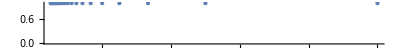

```mathematica
NumberLinePlot[Table[1/n,{n,1,20,1}]]
```

Make a line plot of a list of 100 random integers where the nth integer is between 0 and n. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[RandomInteger[n], {n, 100}]]
```

-Graphics-